```mathematica
folder="C:\\Users\\jacks\\Documents\\GitHub\\cdt_rust\\data\\Analytic_Volume_10_TimeSize_5";files=FileNames["*.csv",folder];
analyticData=Flatten[Import[#]&/@files,1];
```

```mathematica
file="C:\\Users\\jacks\\Documents\\GitHub\\cdt_rust\\data\\Statistical_Volume_10_TimeSize_5.csv";
statisticalDataRaw=Import[file];
```

```mathematica
statisticalData = RandomSample[statisticalDataRaw,10000];
```

```mathematica
statisticalData = statisticalDataRaw;
```

```mathematica
analCounts = Counts[analyticData[[;;,1]]]/Length[analyticData];
keyList = Keys[Sort[analCounts]];
```

```mathematica
statCounts = Counts[statisticalData[[;;,1]]]/Length[statisticalData];
orderedstatCounts=Association@(keyList/. (k_:>(k->statCounts[[k]])));
analCounts = Counts[analyticData[[;;,1]]]/Length[analyticData];
orderedanalCounts=Association@(keyList/. (k_:>(k->analCounts[[k]])));
```

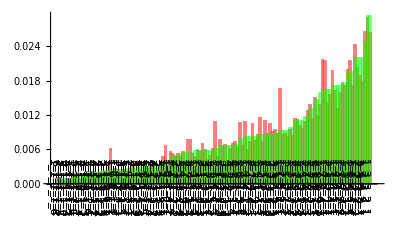

```mathematica
Show[BarChart[orderedstatCounts,ChartLabels->Placed[Automatic,Below,Rotate[#,-Pi/2]&],ChartStyle->Directive[Red,Opacity[0.5]]],
BarChart[orderedanalCounts,ChartLabels->Placed[Automatic,Below,Rotate[#,-Pi/2]&],ChartStyle->Directive[Green,Opacity[0.5]]]]
```

```mathematica
residual = AssociationThread[Keys[analCounts],MapThread[Subtract,{Values[analCounts],Values[statCounts]}]];
```

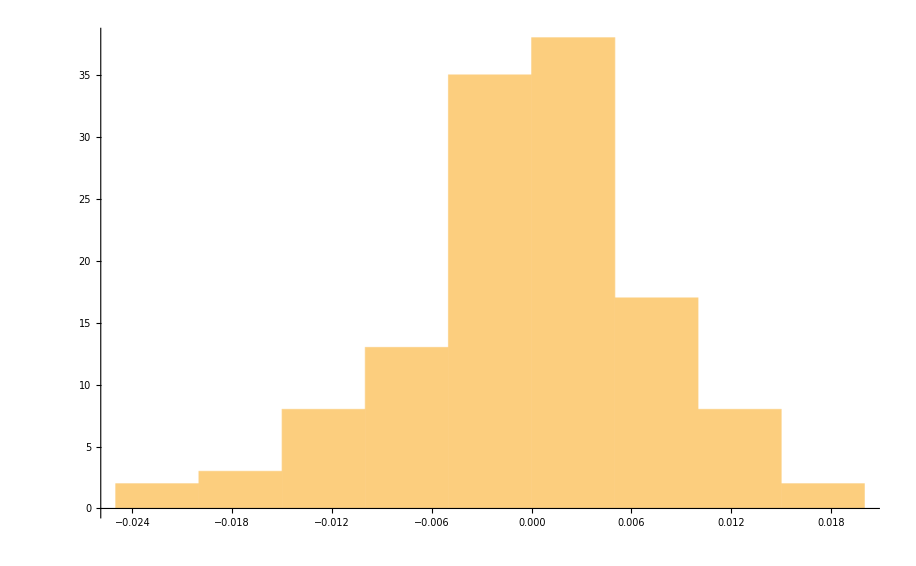

```mathematica
Histogram[residual,10]
```

```mathematica
pValue=KolmogorovSmirnovTest[Values[analCounts],Values[statCounts]]
```

0.807

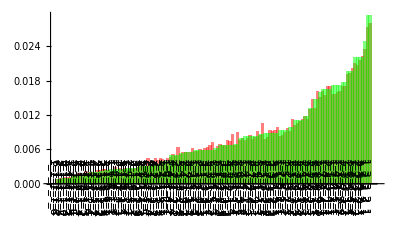

0.98619

```mathematica
keyList = Keys[Sort[analCounts]];
Similarity[statisticalData_]:=Module[{},
statCounts = Counts[statisticalData[[;;,1]]]/Length[statisticalData];
KolmogorovSmirnovTest[Values[analCounts],Values[statCounts]]
]
```

```mathematica
liststatisticalData = tolist[#]&/@statisticalData[[;;,1]]
```

{{1,2,2,3,2},{2,4,1,2,1},{2,3,2,2,1},{1,2,4,2,1},{1,3,3,1,2},{3,1,3,1,2},{6,1,1,1,1},{3,2,2,1,2},{1,2,3,2,2},999982,{1,3,4,1,1},{1,3,1,2,3},{1,1,4,2,2},{1,1,5,1,2},{1,1,5,2,1},{2,1,1,5,1},{2,1,1,4,2},{1,2,1,3,3},{2,3,2,2,1}}
 |  |  |  |

```mathematica
tolist[s_]:=ToExpression[StringSplit[s,"_"]]
```

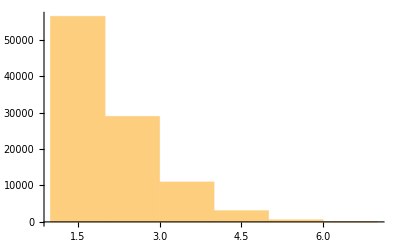
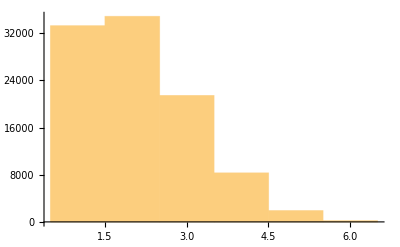
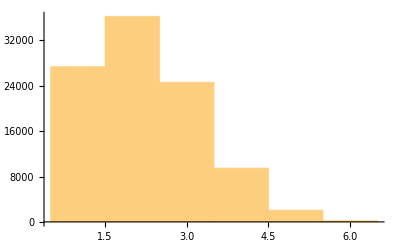
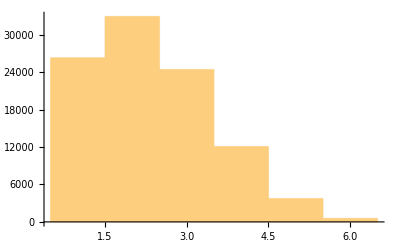
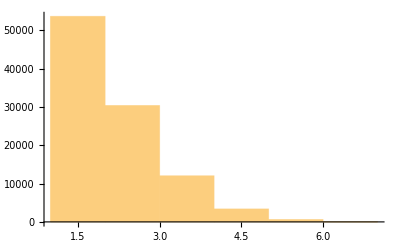
{1→-Graphics-,2→-Graphics-,3→-Graphics-,4→-Graphics-,5→-Graphics-}

```mathematica
Table[i->Histogram[Transpose[liststatisticalData[[;;100000]]][[i]]],{i,5}]
```

```mathematica
data = liststatisticalData[[;;100]];
```